```mathematica
paragraph= "The regulation of artificial intelligence is the development of public sector policies and laws for promoting and regulating artificial intelligence (AI); it is therefore related to the broader regulation of algorithms.
The regulatory and policy landscape for AI is an emerging issue in jurisdictions globally. According to AI Index at Stanford, the annual number of AI-related laws passed in the 127 survey countries jumped from one passed in 2016 to 37 passed in 2022 alone.
Between 2016 and 2020, more than 30 countries adopted dedicated strategies for AI.
Most EU member states had released national AI strategies, as had Canada, China, India, Japan, Mauritius, the Russian Federation, Saudi Arabia, United Arab Emirates, US and Vietnam. Others were in the process of elaborating their own AI strategy, including Bangladesh, Malaysia and Tunisia.
The Global Partnership on Artificial Intelligence was launched in June 2020, stating a need for AI to be developed in accordance with human rights and democratic values, to ensure public confidence and trust in the technology. Henry Kissinger, Eric Schmidt, and Daniel Huttenlocher published a joint statement in November 2021 calling for a government commission to regulate AI. In 2023, OpenAI leaders published recommendations for the governance of superintelligence, which they believe may happen in less than 10 years.In a 2022 Ipsos survey, attitudes towards AI varied greatly by country; 78% of Chinese citizens, but only 35% of Americans, agreed that \"products and services using AI have more benefits than drawbacks\". A 2023 Reuters/Ipsos poll found that 61% of Americans agree, and 22% disagree, that AI poses risks to humanity. In a 2023 Fox News poll, 35% of Americans thought it \"very important\", and an additional 41% thought it \"somewhat important\", for the federal government to regulate AI, versus 13% responding \"not very important\" and 8% responding \"not at all important\".
 ";
```

```mathematica
words=StringSplit[ToLowerCase@StringReplace[paragraph,Except[WordCharacter]->" "]];
```

```mathematica
words=DeleteDuplicates[StringReplace[words,Except[WordCharacter]->""]];
```

```mathematica
functionWords=DeleteStopwords[paragraph];
```

```mathematica
rarityScores=WordFrequencyData[words];
```

```mathematica
rarityScores=ReplaceAll[rarityScores,Missing[___]->0];
```

```mathematica
threshold=0.1; (*Adjust this value as per your definition of rarity*)
rareWords=Select[words,rarityScores[#]<threshold&&!MemberQ[functionWords,#]&];
```

```mathematica
commonWords=WordList[];
```

```mathematica
rareWords=Complement[rareWords,commonWords];
```

```mathematica
rareWords=Select[rareWords,!StringMatchQ[#,NumberString]&];
```

```mathematica
Column[rareWords]
```

ai
algorithms
americans
arab
arabia
attitudes
bangladesh
benefits
broader
canada
chinese
citizens
countries
daniel
drawbacks
elaborating
emirates
eric
eu
henry
huttenlocher
including
india
ipsos
jumped
june
jurisdictions
kissinger
launched
laws
malaysia
mauritius
november
openai
others
passed
policies
poses
products
promoting
recommendations
released
responding
reuters
rights
risks
russian
saudi
schmidt
stanford
states
stating
strategies
superintelligence
tunisia
vietnam

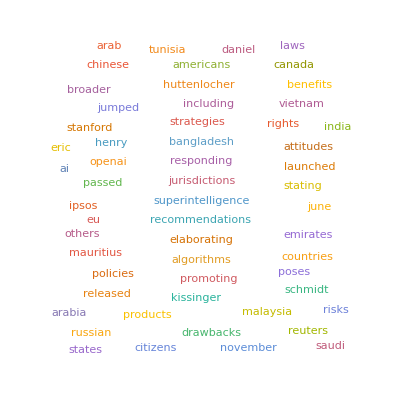

```mathematica
WordCloud[rareWords]
```

```mathematica
wordCounts=Counts[rareWords];
```

```mathematica
matrixSize=Ceiling[Sqrt[Length[wordCounts]]];
matrix=Partition[Values[wordCounts],matrixSize];
```

```mathematica
reliefPlot=ReliefPlot[matrix,ColorFunction->"SunsetColors",FrameTicks->{None,Automatic},ImageSize->500];
```

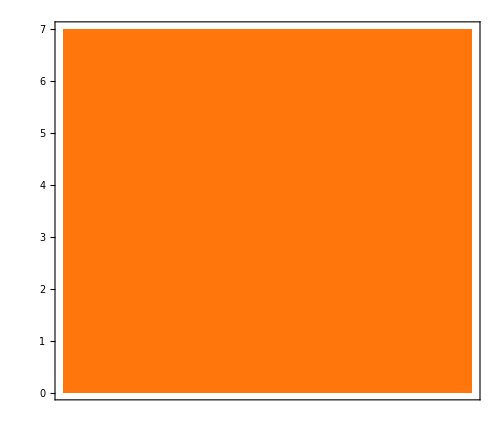

```mathematica
reliefPlot
```